# Probabilités et Statistique II Chapitre 5. Lois discrètes de probabilités

Jamel Saadaoui

University of Strasbourg, BETA,CNRS

https://www.jamelsaadaoui.com/

Discrete Uniform

```mathematica
PDF[DiscreteUniformDistribution[{a,b}],x]
```

Piecewise[{{1/(1-a+b), a≤x≤b}, {0, True}}]

```mathematica
d=DiscreteUniformDistribution[{1,10}]
```

DiscreteUniformDistribution[{1,10}]

```mathematica
PDF[d,x]
```

Piecewise[{{1/10, 1≤x≤10}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{1/10,1≤x≤10}},0]]
```

Piecewise[{{1/10, 1≤x≤10}, {0, True}}]

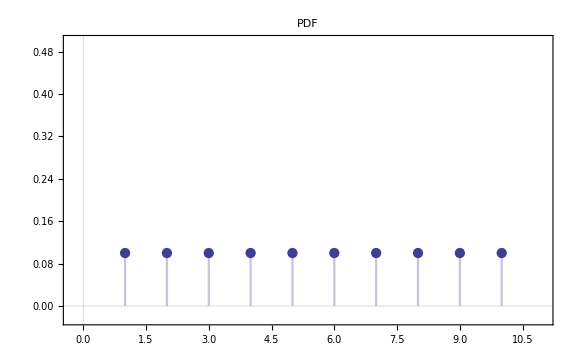

```mathematica
pdf=DiscretePlot[PiecewiseExpand[Piecewise[{{1/10,1≤x≤10}},0]],{x,1,10},ExtentSize->0,PlotLabel->"PDF",PlotStyle->ColorData[1,1],PlotTheme->"Scientific",ImageSize->Large, PlotRange->{{-0.25,11},{-0.025,0.5}}]
```

```mathematica
CDF[d,x]
```

Piecewise[{{Floor[x]/10, 1≤x<10}, {1, x≥10}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{Floor[x]/10,1≤x<10},{1,x≥10}},0]]
```

Piecewise[{{1/10, 1≤x<2}, {1/5, 2≤x<3}, {3/10, 3≤x<4}, {2/5, 4≤x<5}, {1/2, 5≤x<6}, {3/5, 6≤x<7}, {7/10, 7≤x<8}, {4/5, 8≤x<9}, {9/10, 9≤x<10}, {1, x≥10}, {0, True}}]

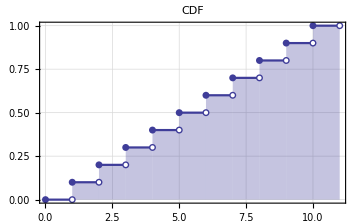

```mathematica
cdf=DiscretePlot[PiecewiseExpand[Piecewise[{{Floor[x]/10,1≤x<10},{1,x≥10}},0]],{x,0,10},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"},PlotLabel->"CDF",PlotStyle->ColorData[1,1],GridLines->Automatic,PlotTheme->"Scientific",ImageSize->Medium]
```

## Mean Discrete Uniform Distribution

The aim is to replicate the demonstration than can be found here : 
https://en.wikibooks.org/wiki/Statistics/Distributions/Discrete_Uniform

The discrete uniform distribution (not to be confused with the continuous uniform distribution) is where the probability of equally spaced possible values is equal. Mathematically this means that the probability density function is identical for a finite set of evenly spaced points. An example of would be rolling a fair 6-sided die. In this case there are six, equally like probabilities.

One common normalization is to restrict the possible values to be integers and the spacing between possibilities to be 1. In this setup, the only two parameters of the function are the minimum value (a), the maximum value (b). (Some even normalize it more, setting a=1.) Let n=b-a+1 be the number of possibilities.

The probability density function is then ∑_(i=0)^n f(x_i)×(x_i):

Let . The mean (noted as ) can then be derived as follows:

```mathematica
EXU=∑_(i=0)^(n-1) (1/n(a+i))
```

1/2 (-1+2 a+n)

```mathematica
Simplify[1/n(∑_(i=0)^(n-1) a+∑_(i=0)^(n-1) i)]
```

1/2 (-1+2 a+n)

Use the Closed Form for Triangular Numbers, with m (m=n-1)

```mathematica
∑_(i=0)^m i
```

1/2 m (1+m)

```mathematica
Expand[(m (1+m))/2==(m+m^2)/2]
```

True

```mathematica
Simplify[1/n(n×a+((n-1)^2+(n-1))/2)]
```

1/2 (-1+2 a+n)

```mathematica
Simplify[(2n×a +n^2-2n+1+n-1)/(2n)]
```

1/2 (-1+2 a+n)

```mathematica
Simplify[(2 a +n-1)/2]
```

1/2 (-1+2 a+n)

```mathematica
(* n=b-a+1 *)
```

```mathematica
n=b-a+1
```

1-a+b

```mathematica
Simplify[(2 a +n-1)/2]
```

(a+b)/2

```mathematica
Mean[DiscreteUniformDistribution[{a,b}]]
```

(a+b)/2

```mathematica
(a+b)/2==(a+b)/3
```

(a+b)/2==(a+b)/3

```mathematica
Expand[%]
```

a/2+b/2==a/3+b/3

```mathematica
(a+b)/2==(a+b)/(1+1)
```

True

```mathematica
Expand[%]
```

True

With variable, the Expand function indicates that the expression are not equivalent by letting the expression intact instead of ‘True’.

```mathematica
Remove[n]
```

```mathematica
Simplify[(2 a +n-1)/2]
```

1/2 (-1+2 a+n)

## Variance Discrete Uniform Distribution

The aim is to replicate the demonstration than can be found here : 
https://en.wikibooks.org/wiki/Statistics/Distributions/Discrete_Uniform

```mathematica
EXU=∑_(i=0)^(n-1) (1/n(a+i))
```

1/2 (-1+2 a+n)

```mathematica
VXU=∑_(i=0)^(n-1) (1/n((a+i)-EXU)^2)
```

1/12 (-1+n^2)

```mathematica
1/n∑_(i=0)^(n-1) ((a+2i-b)/2)^2
```

1/12 (2-6 a+3 a^2+6 b-6 a b+3 b^2-6 n+6 a n-6 b n+4 n^2)

```mathematica
1/(4n)∑_(i=0)^(n-1) (a^2+4a×i-2a×b+4 i^2-4i×b+b^2)
```

1/12 (2-6 a+3 a^2+6 b-6 a b+3 b^2-6 n+6 a n-6 b n+4 n^2)

```mathematica
Simplify[1/(4n)(∑_(i=0)^(n-1) (a^2-2a×b+b^2)+∑_(i=0)^(n-1) (4a×i-4i×b)+∑_(i=0)^(n-1) (4 i^2))]
```

1/12 (2+3 a^2+3 b^2-6 a (1+b-n)-6 b (-1+n)-6 n+4 n^2)

```mathematica
Simplify[1/(4n)(n(a^2-2a×b+b^2)+4(a-b)∑_(i=0)^(n-1) (i)+4∑_(i=0)^(n-1) (i^2))]
```

1/12 (2+3 a^2+3 b^2-6 a (1+b-n)-6 b (-1+n)-6 n+4 n^2)

```mathematica
(1/12) (2+3 a^2+3 b^2-6 a (1+b-n)-6 b (-1+n)-6 n+4 n^2)==(1/12) (2-6 a+3 a^2+6 b-6 a b+3 b^2-6 n+6 a n-6 b n+4 n^2)
```

1/12 (2+3 a^2+3 b^2-6 a (1+b-n)-6 b (-1+n)-6 n+4 n^2)==1/12 (2-6 a+3 a^2+6 b-6 a b+3 b^2-6 n+6 a n-6 b n+4 n^2)

```mathematica
Expand[%]
```

True

Remember that ∑_(i=0)^m (i^2)=[m(m+1)(2m+1)]/6:

```mathematica
∑_(i=0)^m (i^2)
```

1/6 m (1+m) (1+2 m)

```mathematica
Simplify[1/(4n)(n(b-a)^2+4(a-b)(((n-1)n)/2)+4(((n-1)n(2n-1))/6))]
```

1/12 (2+3 (a-b)^2+6 (a-b) (-1+n)-6 n+4 n^2)

```mathematica
%==1/12 (2-6 a+3 a^2+6 b-6 a b+3 b^2-6 n+6 a n-6 b n+4 n^2)
```

1/12 (2+3 (a-b)^2+6 (a-b) (-1+n)-6 n+4 n^2)==1/12 (2-6 a+3 a^2+6 b-6 a b+3 b^2-6 n+6 a n-6 b n+4 n^2)

```mathematica
Expand[%]
```

True

```mathematica
Simplify[1/(4n)(n(n-1)^2-2(n-1)(n-1)n+((2(n-1)n(2n-1))/3))]
```

1/12 (-1+n^2)

```mathematica
(* n=b-a+1 *)
```

```mathematica
n
```

n

```mathematica
Remove[n]
```

```mathematica
Simplify[1/4 (-(-1+n)^2+2/3 (-1+n) (-1+2 n))]
```

1/12 (-1+n^2)

```mathematica
Simplify[1/12(-3(n-1)^2+2(n-1)(2n-1))]
```

1/12 (-1+n^2)

```mathematica
Simplify[1/12(-3(n^2-2n+1)+2(2 n^2-3n+1))]
```

1/12 (-1+n^2)

```mathematica
1/12 (-1+n^2)==(n^2-1)/12
```

True

```mathematica
Expand[%]
```

True

```mathematica
n=b-a+1
```

1-a+b

```mathematica
1-a+b
```

1-a+b

```mathematica
Variance[DiscreteUniformDistribution[{a,b}]]
```

1/12 (-1+(1-a+b)^2)

```mathematica
1/12 (-1+(n)^2)
```

1/12 (-1+(1-a+b)^2)

```mathematica
Remove [n]
```

```mathematica
1/12 (-1+n^2)==(n^2-2)/12
```

1/12 (-1+n^2)==1/12 (-2+n^2)

```mathematica
Expand[%]
```

-1/12+n^2/12==-1/6+n^2/12

With variable, the Expand function indicates that the expression are not equivalent.

Discrete Bernoulli

```mathematica
PDF[BernoulliDistribution[p],x]
```

Piecewise[{{1-p, x==0}, {p, x==1}, {0, True}}]

```mathematica
d=BernoulliDistribution[1/2]
```

BernoulliDistribution[1/2]

```mathematica
PDF[d,x]
```

Piecewise[{{1/2, x==0||x==1}, {0, True}}]

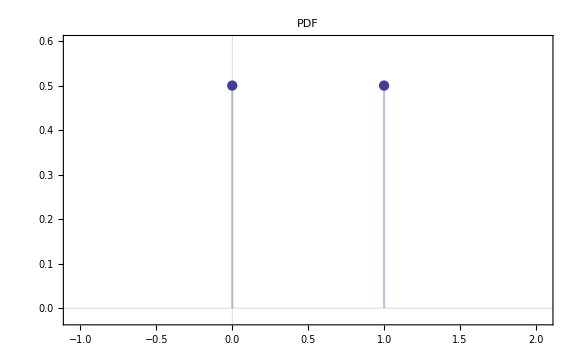

```mathematica
pdf=DiscretePlot[Piecewise[{{1/2,x==0||x==1}},0],{x,0,1},ExtentSize->0,PlotLabel->"PDF",PlotStyle->ColorData[1,1],PlotTheme->"Scientific",ImageSize->Large, PlotRange->{{-1.05,2.05},{-0.025,0.6}}]
```

```mathematica
PiecewiseExpand[Piecewise[{{0,x<0},{1/2,0≤x<1}},1]]
```

Piecewise[{{1/2, 0≤x<1}, {1, x≥1}, {0, True}}]

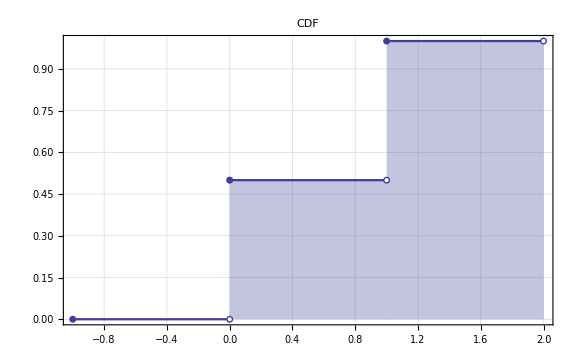

```mathematica
cdf=DiscretePlot[PiecewiseExpand[Piecewise[{{0,x<0},{1/2,0≤x<1}},1]],{x,-1,1},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"},PlotStyle->ColorData[1,1],GridLines->Automatic,PlotLabel->"CDF",PlotTheme->"Scientific",ImageSize->Large]
```

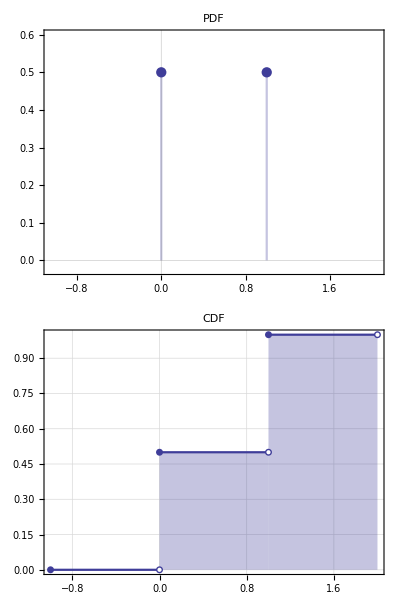

```mathematica
Grid[{{pdf},{cdf}}]
```

Demonstration (Mean)
https://en.wikibooks.org/wiki/Statistics/Distributions/Bernoulli
There is no more basic random event than the flipping of a coin. Heads or tails. It’s as simple as you can get! The “Bernoulli Trial” refers to a single event which can have one of two possible outcomes with a fixed probability of each occurring. You can describe these events as “yes or no” questions. For example:

Will the coin land heads?
Will the newborn child be a girl?
Are a random person's eyes green?
Will a mosquito die after the area was sprayed with insecticide?
Will a potential customer decide to buy my product?
Will a citizen vote for a specific candidate?
Is an employee going to vote pro-union?
Will this person be abducted by aliens in their lifetime?

The Bernoulli Distribution has one controlling parameter: the probability of success. A "fair coin" or an experiment where success and failure are equally likely will have a probability of 0.5 (50%). Typically the variable p is used to represent this parameter.

If a random variable X is distributed with a Bernoulli Distribution with a parameter p we write its probability mass function as:

-Graphics-

This distribution may seem trivial, but it is still a very important building block in probability. The Binomial distribution extends the Bernoulli distribution to encompass multiple "yes" or "no" cases with a fixed probability. Take a close look at the examples cited above. Some similar questions will be presented in the next section which might give an understanding of how these distributions are related.

-Graphics-

```mathematica
p*1+(1-p)*0
```

p

```mathematica
Mean[BernoulliDistribution[p]]
```

p

Demonstration (Variance)
https://en.wikibooks.org/wiki/Statistics/Distributions/Bernoulli
-Graphics-

```mathematica
p*(1-p)^2+(1-p)*(0-p)^2
```

(1-p)^2 p+(1-p) p^2

```mathematica
Factor[(1-p)^2 p+(1-p) p^2]
```

-((-1+p) p)

```mathematica
Simplify[(1-p)^2 p+(1-p) p^2]
```

-((-1+p) p)

```mathematica
Equal[-((-1+p) p)==(1-p) p]
```

True

```mathematica
Variance[BernoulliDistribution[p]]
```

(1-p) p

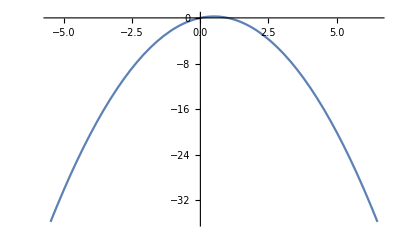

```mathematica
Plot[(1-p) p,{p,-5.5,6.5}]
```

Binomial Distribution

```mathematica
PDF[BinomialDistribution[n,p],x]
```

Piecewise[{{(1-p)^(n-x) p^x Binomial[n,x], 0≤x≤n}, {0, True}}]

```mathematica
d=BinomialDistribution[3,0.95]
```

BinomialDistribution[3,0.95]

```mathematica
PDF[d,x]
```

Piecewise[{{0.05^(3-x) 0.95^x Binomial[3,x], 0≤x≤3}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{0.050000000000000044^(3-x) 0.95^x Binomial[3,x],0≤x≤3}},0]]
```

Piecewise[{{0.000125 19.^x Binomial[3,x], 0≤x≤3}, {0, True}}]

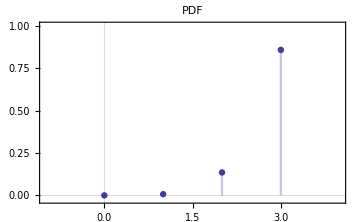

```mathematica
pdf=DiscretePlot[Piecewise[{{0.05^(3-x) 0.95^x Binomial[3,x],0≤x≤3}},0],{x,0,3},ExtentSize->0,PlotLabel->"PDF",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-1,4},{-0.025,1}}]
```

```mathematica
CDF[d,x]
```

Piecewise[{{BetaRegularized[0.05,3-Floor[x],1+Floor[x]], 0≤x<3}, {1, x≥3}, {0, True}}]

```mathematica
cudf=PiecewiseExpand[%]
```

Piecewise[{{0.000125, 0≤x<1}, {0.00725, 1≤x<2}, {0.142625, 2≤x<3}, {1, x≥3}, {0, True}}]

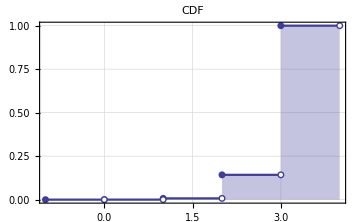

```mathematica
cdf=DiscretePlot[cudf,{x,-0.5,4},ExtentSize->1,ExtentMarkers->{"Filled","Empty"},PlotStyle->ColorData[1,1],PlotLabel->"CDF",GridLines->Automatic,PlotTheme->"Scientific",ImageSize->Medium]
```

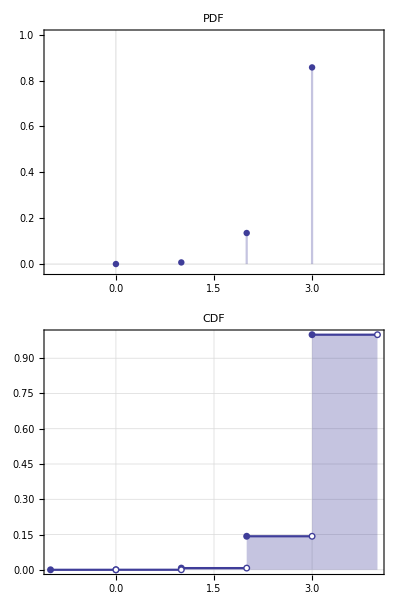

```mathematica
Grid[{{pdf},{cdf}}]
```

## Demonstration (Mean) https://en.wikibooks.org/wiki/Statistics/Distributions/Binomial

```mathematica
(* (1) Write the expression for the Mean:  ∑_(i=0)^n f(Subscript[x, i])×(Subscript[x, i]) *)
```

```mathematica
EX=∑_(x=0)^n Binomial[n,x] p^x(1-p)^(n-x)x;
```

```mathematica
EX==∑_(x=0)^n (n!)/(x!(n-x)!)p^x(1-p)^(n-x)x
```

True

```mathematica
(* (2) The sum start from x=1 *)
```

```mathematica
EX==(n!)/(0!(n-0)!)p^0(1-p)^(n-0)0+∑_(x=0)^n (n!)/(x!(n-x)!)p^x(1-p)^(n-x)x
```

True

```mathematica
(* (3) Replace n! by n(n-1)!, x! by x(x-1)! and simplify x *)
```

```mathematica
EX==∑_(x=1)^n (n(n-1)!)/(x(x-1)!(n-x)!)p^x(1-p)^(n-x)x
```

True

```mathematica
Equal[EX==np∑_(x=1)^n ((n-1)!)/(x(x-1)!(n-x)!)p^(x-1)(1-p)^(n-x)x]
```

True

```mathematica
Equal[EX==np∑_(x=1)^n ((n-1)!)/((x-1)!(n-x)!)p^(x-1)(1-p)^(n-x)]
```

True

```mathematica
(* (4) w=x-1 and m=n-1 *)
```

```mathematica
w=x-1
```

-1+x

```mathematica
m=n-1
```

-1+n

```mathematica
Equal[EX==np∑_(x=1)^n ((m)!)/(w!(m-w)!)p^w(1-p)^(m-w)]
```

True

```mathematica
(* (5) Check that the sum is equal to 1, definition of a PDF *)
```

```mathematica
∑_(x=1)^n ((m)!)/(w!(m-w)!)p^w(1-p)^(m-w)
```

1

```mathematica
(* (6) The demonstration is finished *)
```

```mathematica
EX
```

n p

```mathematica
∑_(x=0)^n Binomial[n,x] p^x(1-p)^(n-x)x
```

n p

```mathematica
Mean[BinomialDistribution[n,p]]
```

n p

Demonstration (Variance)
https://en.wikibooks.org/wiki/Statistics/Distributions/Binomial

```mathematica
(* (1) Write the expression for the "Squared Mean":  ∑_(i=0)^n f(Subscript[x, i])×(Subscript[x, i])^2 *)
```

```mathematica
EX2=∑_(x=0)^n Binomial[n,x] p^x(1-p)^(n-x)x^2;
```

```mathematica
Equal[EX2==∑_(x=0)^n (n!)/(x!(n-x)!)p^x(1-p)^(n-x)x^2]
```

True

```mathematica
(* (2) The sum start from x=1 *)
```

```mathematica
Equal[EX2==(n!)/(0!(n-0)!)p^0(1-p)^(n-0)0+∑_(x=1)^n (n!)/(x!(n-x)!)p^x(1-p)^(n-x)x^2]
```

True

```mathematica
(* (3) Replace n! by n(n-1)!, x! by x(x-1)! and simplify x *)
```

```mathematica
EX2==∑_(x=1)^n (n(n-1)!)/(x(x-1)!(n-x)!)p^x(1-p)^(n-x)x^2
```

True

```mathematica
Equal[EX2==np∑_(x=1)^n ((n-1)!)/((x-1)!(n-x)!)p^(x-1)(1-p)^(n-x)x]
```

True

```mathematica
(* (4) Remind that w=x-1 and m=n-1 *)
```

```mathematica
Equal[EX2==np∑_(x=1)^n ((m)!)/(w!(m-w)!)p^w(1-p)^(m-w)(w+1)]
```

True

```mathematica
Equal[EX2==np∑_(x=1)^n ((m)!)/(w!(m-w)!)p^w(1-p)^(m-w)(w)+np∑_(x=1)^n ((m)!)/(w!(m-w)!)p^w(1-p)^(m-w)]
```

True

```mathematica
(* (5) Check that the sums *)
```

```mathematica
np∑_(x=1)^n ((m)!)/(w!(m-w)!)p^w(1-p)^(m-w)(w)
```

(-1+n) np p

```mathematica
Collect[(-1+n) np p,n]
```

-np p+n np p

```mathematica
np∑_(x=1)^n ((m)!)/(w!(m-w)!)p^w(1-p)^(m-w)
```

np

```mathematica
EX2
```

```mathematica
p (n-n p+n^2 p)
```

p (n-n p+n^2 p)

```mathematica
Equal[p (n-n p+n^2 p)==np(np-p+1)]
```

True

```mathematica
FullSimplify[np(np-p+1)]
```

np (1+np-p)

```mathematica
(* (6) The demonstration is finished *)
```

```mathematica
VX=EX2-(EX)^2
```

-n^2 p^2+p (n-n p+n^2 p)

```mathematica
Simplify[VX]
```

-n (-1+p) p

```mathematica
-n (-1+p) p
```

-n (-1+p) p

```mathematica
Equal[-n (-1+p) p==np(1-p)]
```

True

```mathematica
Variance[BinomialDistribution[n,p]]
```

n (1-p) p

Example 1

```mathematica
BinomialDistribution[3,0.95]
```

BinomialDistribution[3,0.95]

```mathematica
PDF[BinomialDistribution[3,0.95],x]
```

Piecewise[{{0.05^(3-x) 0.95^x Binomial[3,x], 0≤x≤3}, {0, True}}]

```mathematica
Table[Piecewise[{{0.050000000000000044^(3-x) 0.95^x Binomial[3,x],0≤x≤3}},0],{x,1,20}]
```

{0.007125,0.135375,0.857375,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
PiecewiseExpand[Piecewise[{{0.050000000000000044^(3-x) 0.95^x Binomial[3,x],0≤x≤3}},0]]
```

Piecewise[{{0.000125 19.^x Binomial[3,x], 0≤x≤3}, {0, True}}]

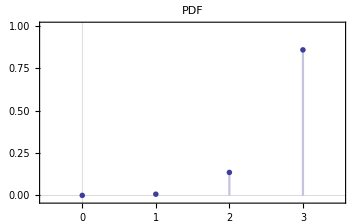

```mathematica
DiscretePlot[Piecewise[{{0.00012500000000000033 18.999999999999982^x Binomial[3,x],0≤x≤3}},0],{x,0,20},ExtentSize->0,PlotLabel->"PDF",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-.5,3.5},{-0.025,1}}]
```

Example 2

```mathematica
PDF[BinomialDistribution[5,0.90],x]
```

Piecewise[{{0.1^(5-x) 0.9^x Binomial[5,x], 0≤x≤5}, {0, True}}]

```mathematica
Table[Piecewise[{{0.09999999999999998^(5-x) 0.9^x Binomial[5,x],0≤x≤5}},0],{x,0,5}]
```

{0.00001,0.00045,0.0081,0.0729,0.32805,0.59049}

```mathematica
mean=(0.00001*0)+(0.00045*1)+(0.0081*2)+(0.0729*3)+(0.32805*4)+(0.59049*5)
```

4.5

```mathematica
variance=(0.00001*0^2)+(0.00045*1^2)+(0.0081*2^2)+(0.0729*3^2)+(0.32805*4^2)+(0.59049*5^2)-mean^2
```

0.45

```mathematica
PiecewiseExpand[Piecewise[{{0.09999999999999998^(5-x) 0.9^x Binomial[5,x],0≤x≤5}},0]]
```

Piecewise[{{0.00001 9.^x Binomial[5,x], 0≤x≤5}, {0, True}}]

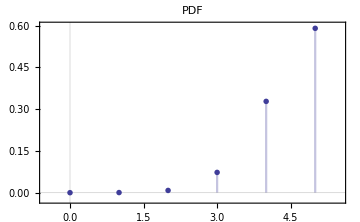

```mathematica
DiscretePlot[Piecewise[{{9.999999999999987*^-6 9.000000000000002^x Binomial[5,x],0≤x≤5}},0],{x,0,20},ExtentSize->0,PlotLabel->"PDF",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-.5,5.5},{-0.025,0.6}}]
```

Poisson Distribution

```mathematica
PDF[PoissonDistribution[λ],x]
```

Piecewise[{{(ⅇ^-λ λ^x)/(x!), x≥0}, {0, True}}]

```mathematica
d=PoissonDistribution[1.5]
```

PoissonDistribution[1.5]

```mathematica
PDF[d,x]
```

Piecewise[{{(0.22313 1.5^x)/(x!), x≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{(0.22313016014842982 1.5^x)/(x!),x≥0}},0]]
```

Piecewise[{{(0.22313 1.5^x)/(x!), x≥0}, {0, True}}]

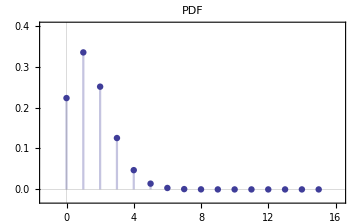

```mathematica
pdf=DiscretePlot[Piecewise[{{(0.22313016014842982 1.5^x)/(x!),x≥0}},0],{x,0,15},ExtentSize->0,PlotLabel->"PDF",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-1.25,16.25},{-0.025,0.4}}]
```

```mathematica
CDF[d,x]
```

Piecewise[{{GammaRegularized[1+Floor[x],1.5], x≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{GammaRegularized[1+Floor[x],1.5],x≥0}},0]]
```

Piecewise[{{GammaRegularized[1+Floor[x],1.5], x≥0}, {0, True}}]

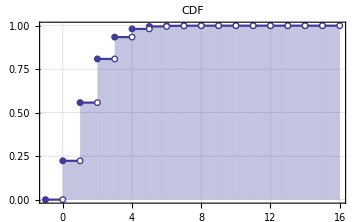

```mathematica
cdf=DiscretePlot[PiecewiseExpand[Piecewise[{{GammaRegularized[1+Floor[x],1.5],x≥0}},0]],{x,-1,15},ExtentSize->Right,ExtentMarkers->{"Filled","Empty"},PlotLabel->"CDF",GridLines->Automatic,PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium]
```

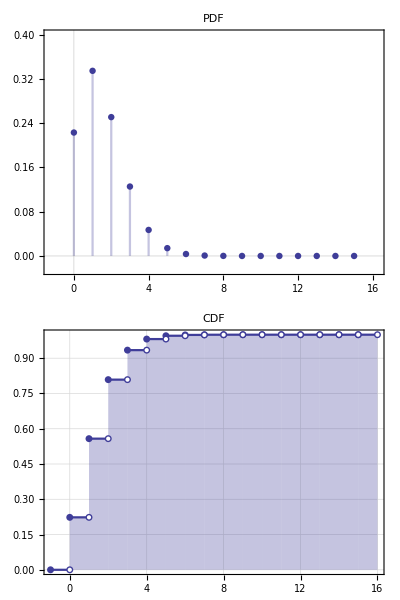

```mathematica
Grid[{{pdf},{cdf}}]
```

Demonstration (Mean)
https://en.wikibooks.org/wiki/Statistics/Distributions/Poisson
-Graphics-

```mathematica
∑_(x=0)^∞ (ⅇ^-λ λ^x)/(x!)x
```

λ

```mathematica
Sum[(ⅇ^-λ λ^x)/(x!)x,{x,0,∞}]
```

λ

Demonstration (Variance)
https://en.wikibooks.org/wiki/Statistics/Distributions/Poisson ; https://proofwiki.org/wiki/Variance_of_Poisson_Distribution
-Graphics-

```mathematica
∑_(x=0)^∞ (ⅇ^-λ λ^x)/(x!)x^2
```

λ+λ^2

```mathematica
Variance[PoissonDistribution[λ]]
```

λ

### Example 1

```mathematica
PoissonDistribution[2]
```

```mathematica
PoissonDistribution[2]
```

PoissonDistribution[2]

```mathematica
PDF[PoissonDistribution[2],x]
```

Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{2^x/(ⅇ^2 x!),x≥0}},0]]
```

Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}]

```mathematica
a=Table[Piecewise[{{2^x/(ⅇ^2 x!),x≥0}},0],{x,0,10}]
b=Table[Piecewise[{{x,x≥0}},0],{x,0,10}]
c=N[a,4]
```

{1/ⅇ^2,2/ⅇ^2,2/ⅇ^2,4/(3 ⅇ^2),2/(3 ⅇ^2),4/(15 ⅇ^2),4/(45 ⅇ^2),8/(315 ⅇ^2),2/(315 ⅇ^2),4/(2835 ⅇ^2),4/(14175 ⅇ^2)}

{0,1,2,3,4,5,6,7,8,9,10}

{0.1353,0.2707,0.2707,0.1804,0.09022,0.03609,0.01203,0.003437,0.0008593,0.0001909,0.00003819}

```mathematica
acol=Column[a];
bcol=Column[b];
Grid[{b,c}]
```

0 | 1 | 2 | 3 | 4 | 5 | 6 | 7 | 8 | 9 | 10
0.1353 | 0.2707 | 0.2707 | 0.1804 | 0.09022 | 0.03609 | 0.01203 | 0.003437 | 0.0008593 | 0.0001909 | 0.00003819

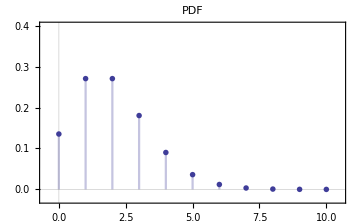

```mathematica
DiscretePlot[Piecewise[{{2^x/(ⅇ^2 x!),x≥0}},0],{x,0,20},ExtentSize->0,PlotLabel->"PDF",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-.5,10.5},{-0.025,0.4}}]
```

Example 2

```mathematica
PoissonDistribution[2]
```

PoissonDistribution[2]

```mathematica
dist=TransformedDistribution[x+y,{x\[Distributed]PoissonDistribution[2],y\[Distributed]PoissonDistribution[1]}];
```

```mathematica
Mean[dist]
```

3

```mathematica
PDF[PoissonDistribution[2],x]
```

Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}]

```mathematica
PDF[PoissonDistribution[2],2]
```

2/ⅇ^2

```mathematica
N[2/ⅇ^2]
```

0.270671

```mathematica
Mean[PoissonDistribution[2]]
```

2

```mathematica
PoissonDistribution[1]
```

PoissonDistribution[1]

```mathematica
PDF[PoissonDistribution[1],x]
```

Piecewise[{{1/(ⅇ x!), x≥0}, {0, True}}]

```mathematica
PDF[PoissonDistribution[1],2]
```

1/(2 ⅇ)

```mathematica
N[1/(2 ⅇ)]
```

0.18394

```mathematica
PoissonDistribution[3]
```

PoissonDistribution[3]

```mathematica
PDF[PoissonDistribution[3],x]
```

Piecewise[{{3^x/(ⅇ^3 x!), x≥0}, {0, True}}]

```mathematica
PDF[PoissonDistribution[3],2]
```

9/(2 ⅇ^3)

```mathematica
3^2/(ⅇ^3 2!)
```

9/(2 ⅇ^3)

```mathematica
N[9/(2 ⅇ^3)]
```

0.224042

```mathematica
Mean[PoissonDistribution[3]]
```

3

Proxy Binomial and Poisson

```mathematica
BinomialDistribution[100,0.02]
```

BinomialDistribution[100,0.02]

```mathematica
PDF[BinomialDistribution[100,0.02],x]
```

Piecewise[{{0.02^x 0.98^(100-x) Binomial[100,x], 0≤x≤100}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{0.02^x 0.98^(100-x) Binomial[100,x],0≤x≤100}},0]]
```

Piecewise[{{0.13262 0.0204082^x Binomial[100,x], 0≤x≤100}, {0, True}}]

```mathematica
Table[Piecewise[{{0.13261955589475277 0.020408163265306124^x Binomial[100,x],0≤x≤100}},0],{x,0,6}]
```

{0.13262,0.270652,0.273414,0.182276,0.090208,0.0353468,0.0114216}

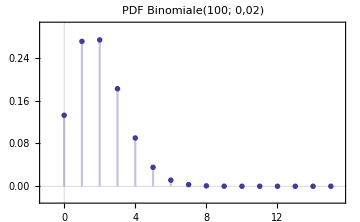

```mathematica
binomiale=DiscretePlot[Piecewise[{{0.13261955589475277 0.020408163265306124^x Binomial[100,x],0≤x≤100}},0],{x,0,20},ExtentSize->0,PlotLabel->"PDF Binomiale(100; 0,02)",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-1.05,15.5},{-0.025,0.3}}]
```

```mathematica
PoissonDistribution[2]
```

PoissonDistribution[2]

```mathematica
PDF[PoissonDistribution[2],x]
```

Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}]

```mathematica
PiecewiseExpand[Piecewise[{{2^x/(ⅇ^2 x!),x≥0}},0]]
```

Piecewise[{{2^x/(ⅇ^2 x!), x≥0}, {0, True}}]

```mathematica
N[Table[Piecewise[{{2^x/(ⅇ^2 x!),x≥0}},0],{x,0,6}]]
```

{0.135335,0.270671,0.270671,0.180447,0.0902235,0.0360894,0.0120298}

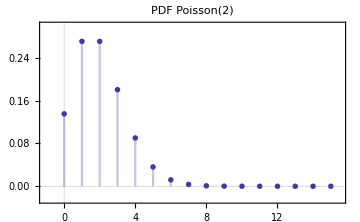

```mathematica
poisson=DiscretePlot[Piecewise[{{2^x/(ⅇ^2 x!),x≥0}},0],{x,0,20},ExtentSize->0,PlotLabel->"PDF Poisson(2)",PlotStyle->ColorData[1,1], PlotTheme->"Scientific",ImageSize->Medium, PlotRange->{{-1.05,15.5},{-0.025,0.3}}]
```

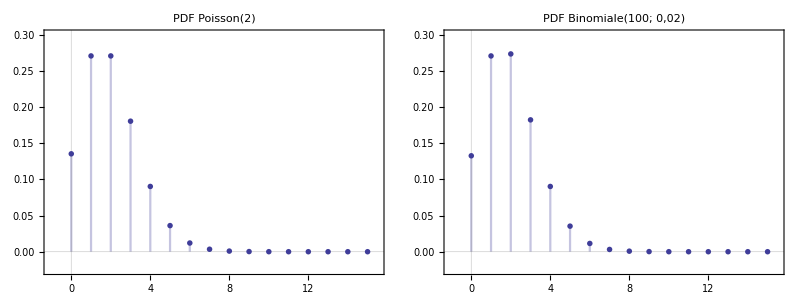

```mathematica
TableForm[Table[{poisson,binomiale},1]]
```